```mathematica
OneBitChanges[list_]:= Table[MapAt[1-#&,list,{1}],{i,Length[list]}]
```

```mathematica
OneBitChanges[{1,0,1}]
```

{{0,0,1},{0,0,1},{0,0,1}}

```mathematica
n=2
```

2

Flatten::fldep: Level 1 specified in {{1,0,1}} exceeds the levels, 0, which can be flattened together in OneBitChanges[#1]&.

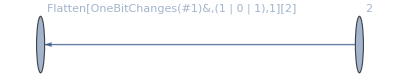

```mathematica
NestGraph[Flatten[OneBitChanges[#]&,{{1,0,1}},1],2,VertexLabels->Automatic]
```

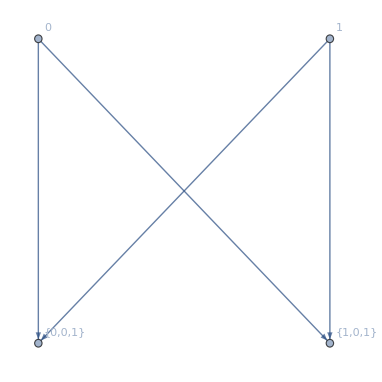

```mathematica
NestGraph[Flatten[#,1]&/@OneBitChanges[#]&,{{1,0,1}},3,VertexLabels->Automatic]
```

```mathematica
Flatten[OneBitChanges[OneBitChanges[OneBitChanges[{1,0,1}]]],1]
```

{{{0,0,1},{1,1,0},{1,1,0}},{{1,1,0},{0,0,1},{0,0,1}},{{1,1,0},{0,0,1},{0,0,1}},{{0,0,1},{1,1,0},{1,1,0}},{{1,1,0},{0,0,1},{0,0,1}},{{1,1,0},{0,0,1},{0,0,1}},{{0,0,1},{1,1,0},{1,1,0}},{{1,1,0},{0,0,1},{0,0,1}},{{1,1,0},{0,0,1},{0,0,1}}}